```mathematica
pp= 1.35;
NU= Flatten[{Table[0.002 pp^n,{n,0,28,1}],Infinity}];
```

### Without resource aggregation

```mathematica
localfolder = "C:\\Users\\tramiada\\Documents\\Projects\\et3\\sim1\\";
```

```mathematica
result1= {};
Do[
repl= {};
Do[data = Import[localfolder<>"sim_est_z_1_aggreg_0.5_M_1_com_id_"<>ToString@id<>"_size_12_T_4000_muR_0.1_lambda_0.2_gH_1_replicates_"<>ToString@rep<>".csv"];
temp = data[[-3]]; (* -1 is time, -2 is empty*)
AppendTo[repl,{ NU[[id+1]],If[temp[[1]]==10,Infinity,π temp[[2]]^2  temp[[1]] temp[[3]]]}];
,{rep,0,9,1}];
AppendTo[result1,repl];
,{id,0,29,1}];
```

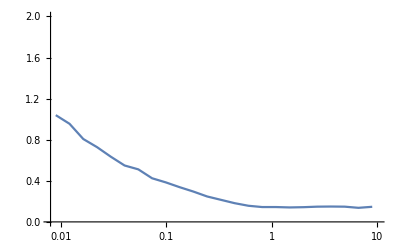

```mathematica
mean1 = Map[Mean,result1];
ListLogLinearPlot[mean1,PlotRange->{{0.008,10},{0,2}},Joined->True,AxesOrigin->{0.008,0}]
```

```mathematica
R1 = {}; R2 = {};
Do[
temp = result1[[ii]];
pos =  Partition[Position[temp,Infinity][[All,1]],1];
temp2 = Delete[temp,pos];
If[Length[temp2] ≤ 1, 
res = {NU[[ii]],Infinity};
res1  ={NU[[ii]],Infinity},
res = {NU[[ii]],StandardDeviation[temp2[[All,2]]]};
res1  ={NU[[ii]],StandardDeviation[temp2[[All,2]]]/Mean[temp2[[All,2]]]};
];
AppendTo[R1, res];
AppendTo[R2, res1];
,{ii, Length[result1]}];
```

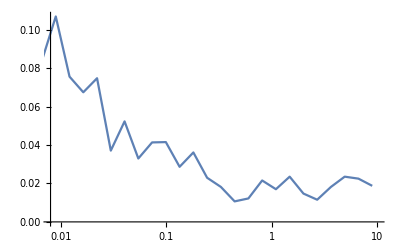

```mathematica
ListLogLinearPlot[R1,PlotRange->{{0.008,10},{0,All}},Joined->True,AxesOrigin->{0.008,0}]
```

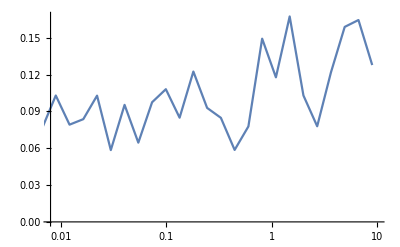

```mathematica
ListLogLinearPlot[R2,PlotRange->{{0.008,10},{0,All}},Joined->True,AxesOrigin->{0.008,0}]
```

### With resource aggregation

```mathematica
result2= {};
Do[
repl= {};
Do[data = Import[localfolder<>"sim_est_z_1_aggreg_0_M_1_com_id_"<>ToString@id<>"_size_12_T_4000_muR_0.1_lambda_0.2_gH_1_replicates_"<>ToString@rep<>".csv"];
temp = data[[-3]]; (* -1 is time, -2 is empty*)
AppendTo[repl,{ NU[[id+1]],If[temp[[1]]==10,Infinity,π temp[[2]]^2  temp[[1]] temp[[3]]]}];
,{rep,0,9,1}];
AppendTo[result2,repl];
,{id,0,29,1}];
```

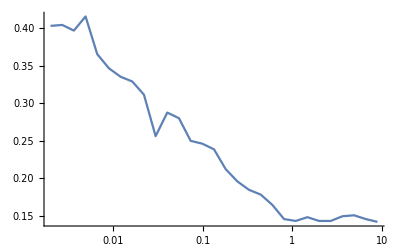

```mathematica
mean2 = Map[Mean,result2];
ListLogLinearPlot[mean2,PlotRange->{{0.008,10},{2,0}},Joined->True,AxesOrigin->{0.008,0}]
```

```mathematica
R3 = {}; R4 = {};
Do[
temp = result2[[ii]];
pos =  Partition[Position[temp,Infinity][[All,1]],1];
temp2 = Delete[temp,pos];
If[Length[temp2] ≤ 1, 
res = {NU[[ii]],Infinity};
res1 = {NU[[ii]],Infinity},
res = {NU[[ii]],StandardDeviation[temp2[[All,2]]]};
res1  ={NU[[ii]],StandardDeviation[temp2[[All,2]]]/Mean[temp2[[All,2]]]};
];
AppendTo[R3, res];
AppendTo[R4, res1];
,{ii, Length[result2]}];
```

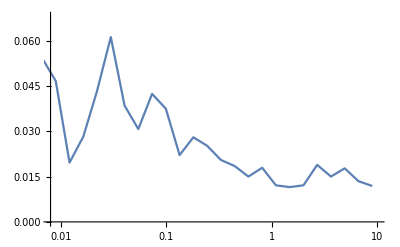

```mathematica
ListLogLinearPlot[R3,PlotRange->{{0.008,10},{0,All}},Joined->True,AxesOrigin->{0.008,0}]
```

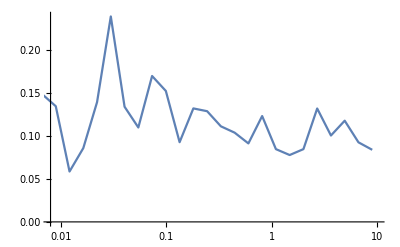

```mathematica
ListLogLinearPlot[R4,PlotRange->{{0.008,10},{0,All}},Joined->True,AxesOrigin->{0.008,0}]
```